# ME: Trabalho Computacional

## 99405 Clara Pereira 99407 Diana Gaspar 99423 Madalena Preto 99441 Samuel Pearson 99447 Vasco Reigadas

## Problema 1

### (a)

Como n == 2^a * t + 1 .  Temos que: b ^ ( n - 1 ) - 1 == b ^ ( 2 ^ a * t + 1) - 1

```mathematica
Simplify[(b^t-1)(b^t+1)(b^(2t)+1)(b^(4t)+1)(b^(8t)+1)]
```

-1+b^(16 t)

```mathematica
Simplify[(b^(16t)-1)(b^(16t)+1)(b^(32t)+1)(b^(64t)+1)]
```

-1+b^(128 t)

. . .

```mathematica
Simplify[(b^(2^(a-2)t)-1)(b^(2^(a-2)t)+1)]
```

-1+b^(2^(-1+a) t)

```mathematica
Simplify[(b^(2^(a-1)t)-1)(b^(2^(a-1)t)+1)]
```

-1+b^(2^a t)

Como b ^ ( 2 ^ a * t + 1) - 1 == b ^ ( n - 1 ) - 1 , está provada a equivalência.

```mathematica
pseudoprimo[n_Integer, b_Integer]:=
If[Mod[b^(n-1),n]==1, True, False]
```

```mathematica
pseudoequiv[base_Integer,exp_Integer,coef_Integer]:=
Module[{n,x,y}, n= 2^exp * coef+1 ;
x= base^(n-1)-1;
y = (base^coef-1)*Product[base^(2^p*coef)+1, {p, 0, exp-1}];
If[x==y, Return[True], Return[False]]]
```

```mathematica
pseudoequivfinal[base_Integer,exp_Integer,coef_Integer]:=
If[pseudoprimo[2^exp*coef+1,base]==pseudoequiv[base,exp,coef], Return[True], Return[False]]
```

Para alguns pseudoprimos em base 2 compostos:

```mathematica
Select[Select[Range[300,3000], Function[x,pseudoprimo[x,2]]], CompositeQ]
```

{341,561,645,1105,1387,1729,1905,2047,2465,2701,2821}

```mathematica
341 == 340 + 1 == 2^2 * 85 + 1;
pseudoequivfinal[2,2,85]
```

True

```mathematica
2047 == 2046 + 1 == 2^1*1023+1;
pseudoequivfinal[2,1,1023]
```

True

Para alguns números não pseudoprimos (não se encontram na lista previamente definida) em base 2:

```mathematica
1239 == 2^1*617+1;
pseudoequiv[2,1,619]
```

True

```mathematica
2441== 2^3*305+1;
pseudoequivfinal[2,3,305]
```

True

### (b)

```mathematica
pseudopforte[n_Integer/;n≥3&&OddQ[n],b_Integer/;b≥2]/;
GCD[b,n]==1:=
Module[{t,a,x,i},
t=n-1;
a=0;
While[EvenQ[t],
t=t/2;
a=a+1];
x=PowerMod[b,t,n];
If[x==1||x==n-1,
Return[True],
For[i=1,i≤a-1,i++,
x=Mod[x*x,n];
If[x==n-1,
Return[True]]];
Return[False]]]
```

```mathematica
pseudopforte[341,2]
```

False

```mathematica
pseudopforte[873,2]
```

False

```mathematica
pseudopforte[2047,2]
```

True

### (c)

```mathematica
candidatos6 =  Complement[Range[2,10^6], Prime[Range[PrimePi[10^6]]]];
listapseudoprimos6 = Select[candidatos6, Function[x, pseudoprimo[x,2]]];
```

Cálculo do primeiro pseudoprimo composto em base 2:

```mathematica
Part[listapseudoprimos6, 1]
```

341

Cálculo do número de pseudoprimos em base 2 até 10^6:

```mathematica
Length[listapseudoprimos6]
```

245

Cálculo do número de pseudoprimos fortes em base 2 até 10^6:

```mathematica
listafortes6 = Select[listapseudoprimos6, Function[x,pseudopforte[x,2]]];
Length[listafortes6]
```

46

```mathematica
pseudopforte[389,2]
```

True

O programa seguinte demora cerca de 2 horas e meia a avaliar.

```mathematica
candidatos7 =  Complement[Range[2,10^7], Prime[Range[PrimePi[10^7]]]];
listapseudoprimos7 = Select[candidatos7, Function[x, pseudoprimo[x,2]]];
```

Cálculo do número de pseudoprimos em base 2 até 10^7:

```mathematica
Length[listapseudoprimos7]
```

750

```mathematica
listafortes7 = Select[listapseudoprimos7, Function[x,pseudopforte[x,2]]];
Length[listafortes7]
```

162

O programa seguinte não foi avaliado, estima-se que demore horas a correr. Deveria avaliar o número de pseudoprimos em base 2 até 10^9.

```mathematica
candidatos9 =  Complement[Range[2,10^9], Prime[Range[PrimePi[10^9]]]];
listapseudoprimos9 = Select[candidatos9, Function[x, pseudoprimo[x,2]]];
Length[listapseudoprimos9]
```

$Aborted

5597

O programa seguinte não foi avaliado, depende do programa anterior. Deveria avaliar o número de pseudoprimos fortes em base 2 até 10^9.

```mathematica
listafortes9 = Select[listapseudoprimos9, Function[x,pseudopforte[x,2]]];
Length[listafortes9]
```

$Aborted

### (d)

Cálculo do número de pseudoprimos em bases 2, 3, 5 e 7 até 10^7:

```mathematica
lista7pseudoprimos2e3 = Select[listapseudoprimos7, Function[x, pseudoprimo[x,3]]];
lista7pseudoprimos2e3e5 = Select[lista7pseudoprimos2e3, Function[x, pseudoprimo[x,5]]];
lista7pseudoprimos2e3e5e7 = Select[lista7pseudoprimos2e3e5, Function[x,pseudoprimo[x,7]]];
Length[lista7pseudoprimos2e3e5e7]
```

63

Cálculo do número de pseudoprimos fortes em base 2, 3, 5 e 7 até 10^7:

```mathematica
lista7fortes2 = Select[lista7pseudoprimos2e3e5e7, Function[x, pseudopforte[x,2]]];
lista7fortes2e3 = Select[lista7fortes2, Function[x, pseudopforte[x,3]]];
lista7fortes2e3e5 = Select[lista7fortes2e3, Function[x, pseudopforte[x,5]]];
lista7fortes2e3e5e7 = Select[lista7fortes2e3e5, Function[x, pseudopforte[x,7]]]
```

{}

O programa seguinte não foi avaliado, depende de um programa anterior não avaliado. Deveria avaliar o número de pseudoprimos fortes nas bases 2, 3, 5 e 7 até 10^9.

```mathematica
lista9pseudoprimos2e3 = Select[listapseudoprimos9, Function[x, pseudoprimo[x,3]]];
lista9pseudoprimos2e3e5 = Select[lista9pseudoprimos2e3, Function[x, pseudoprimo[x,5]]];
lista9pseudoprimos2e3e5e7 = Select[lista9pseudoprimos2e3e5, Function[x,pseudoprimo[x,7]]];
Length[lista9pseudoprimos2e3e5e7]
```

$Aborted

1770

O programa seguinte não foi avaliado, depende do programa anterior. Deveria avaliar o conjunto de pseudoprimos fortes nas base 2, 3, 5 e 7 até 10^9.

```mathematica
lista9fortes2 = Select[lista9pseudoprimos2e3e5e7, Function[x, pseudopforte[x,2]]];
lista9fortes2e3 = Select[lista9fortes2, Function[x, pseudopforte[x,3]]];
lista9fortes2e3e5 = Select[lista9fortes2e3, Function[x, pseudopforte[x,5]]];
lista9fortes2e3e5e7 = Select[lista9fortes2e3e5, Function[x, pseudopforte[x,7]]]
```

$Aborted

{3215031751}

Confirmação que 3 215 031 751 é pseudoprimo forte em base 2, 3, 5 e 7:

```mathematica
pseudopforte[3215031751, 2]
```

True

```mathematica
pseudopforte[3215031751, 3]
```

True

```mathematica
pseudopforte[3215031751, 5]
```

True

```mathematica
pseudopforte[3215031751, 7]
```

True

### (e)

```mathematica
googol0 = Select[Range[0,1000], Function[x, pseudoprimo[10^100+x, 2]]]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

{}

```mathematica
googol1 = Select[Range[0,1000], Function[x, pseudopforte[x+10^100, 2]]];
googol2 = Map[Function[x, HoldForm[10^100+x]],googol1]
```

{10^100+267,10^100+949}

```mathematica
PrimeQ[10^100+267]
```

True

```mathematica
PrimeQ[10^100+949]
```

True

### (f)

```mathematica
carmichael[x_Integer/;CompositeQ[x]&&OddQ[x]]:=
AllTrue[Select[Range[2,x-1], Function[y, CoprimeQ[y,x]]],
Function[i, pseudoprimo[x,i]]]
```

```mathematica
listacarmichael= Select[Range[10000], carmichael]
```

{561,1105,1729,2465,2821,6601,8911}

```mathematica
listaquatrofatores = Select[listacarmichael, Function[x, PrimeNu[x]]==4]
```

{}

```mathematica
listacarmichael= Select[Range[10000], carmichael]
```

{561,1105,1729,2465,2821,6601,8911}

O programa seguinte demora cerca de 2 minutos a avaliar.

```mathematica
carmichael[41041]
```

True

```mathematica
PrimeNu[41041]==4
```

True

### (g)

```mathematica
carmichael2[n_Integer/;CompositeQ[n]&&OddQ[n]]:=
Module[{div, sqrt, primediv, primediv2},
div= Select[Divisors[n], Function[x, x≠1]];
sqrt = Select[div, Function[x, IntegerQ[Sqrt[x]]]];
primediv = Select[div, PrimeQ];
primediv2 = Select[primediv, Function[p, Mod[n-1,p-1]==0]];
If[0==Length[sqrt]
&& Length[primediv]==Length[primediv2],
Return[True],
Return[False]]]
```

```mathematica
listacarmichael2 = Select[Range[10000], carmichael2]
```

{561,1105,1729,2465,2821,6601,8911}

O programa seguinte demora cerca de 23 minutos a avaliar.

```mathematica
Timing[listacarmichael= Select[Range[50000], carmichael]]
```

{1357.57,{561,1105,1729,2465,2821,6601,8911,10585,15841,29341,41041,46657}}

```mathematica
Timing[Select[Range[50000], carmichael2]]
```

{1.96694,{561,1105,1729,2465,2821,6601,8911,10585,15841,29341,41041,46657}}

## Problema 2

```mathematica
residuoQ[b_Integer,p_Integer/;PrimeQ[p]]/;(GCD[b,p]==1):=
PowerMod[b,(p-1)/2,p]==1
```

### (a)

```mathematica
afirmacao[c_Integer,d_Integer,p_Integer/;PrimeQ[p]]:=
Equivalent[residuoQ[c*d,p],(residuoQ[c,p]&&residuoQ[d,p])||(!residuoQ[c,p]&&!residuoQ[d,p])]
```

O programa seguinte avalia até z-1 pois x != z e y != z.

```mathematica
Grid[Flatten[Table[{{x,y,z},afirmacao[x,y,z]},{z,{2,3,5,7}},{x,1,z-1},{y,1,z-1}],1]]
```

{{1,1,2},True} |  |  |  |  | 
{{1,1,3},True} | {{1,2,3},True} |  |  |  | 
{{2,1,3},True} | {{2,2,3},True} |  |  |  | 
{{1,1,5},True} | {{1,2,5},True} | {{1,3,5},True} | {{1,4,5},True} |  | 
{{2,1,5},True} | {{2,2,5},True} | {{2,3,5},True} | {{2,4,5},True} |  | 
{{3,1,5},True} | {{3,2,5},True} | {{3,3,5},True} | {{3,4,5},True} |  | 
{{4,1,5},True} | {{4,2,5},True} | {{4,3,5},True} | {{4,4,5},True} |  | 
{{1,1,7},True} | {{1,2,7},True} | {{1,3,7},True} | {{1,4,7},True} | {{1,5,7},True} | {{1,6,7},True}
{{2,1,7},True} | {{2,2,7},True} | {{2,3,7},True} | {{2,4,7},True} | {{2,5,7},True} | {{2,6,7},True}
{{3,1,7},True} | {{3,2,7},True} | {{3,3,7},True} | {{3,4,7},True} | {{3,5,7},True} | {{3,6,7},True}
{{4,1,7},True} | {{4,2,7},True} | {{4,3,7},True} | {{4,4,7},True} | {{4,5,7},True} | {{4,6,7},True}
{{5,1,7},True} | {{5,2,7},True} | {{5,3,7},True} | {{5,4,7},True} | {{5,5,7},True} | {{5,6,7},True}
{{6,1,7},True} | {{6,2,7},True} | {{6,3,7},True} | {{6,4,7},True} | {{6,5,7},True} | {{6,6,7},True}

### (b)

```mathematica
primosnmax[b_Integer/;PrimeQ[b],nmax_Integer/;nmax≥3]:= 
Select[Select[Range[3,nmax],PrimeQ],Function[x,residuoQ[b,x]]]
```

```mathematica
tabela=Grid[Table[{i,primosnmax[i,100]},{i,{2,3,5,7,11,13,17}}],Frame->All]
```

2 | {7,17,23,31,41,47,71,73,79,89,97}
3 | {11,13,23,37,47,59,61,71,73,83,97}
5 | {11,19,29,31,41,59,61,71,79,89}
7 | {3,19,29,31,37,47,53,59,83}
11 | {5,7,19,37,43,53,79,83,89,97}
13 | {3,17,23,29,43,53,61,79}
17 | {13,19,43,47,53,59,67,83,89}

```mathematica
ReplacePart[tabela,1->Prepend[First[tabela],{"b","Lista"}]]
```

b | Lista
2 | {7,17,23,31,41,47,71,73,79,89,97}
3 | {11,13,23,37,47,59,61,71,73,83,97}
5 | {11,19,29,31,41,59,61,71,79,89}
7 | {3,19,29,31,37,47,53,59,83}
11 | {5,7,19,37,43,53,79,83,89,97}
13 | {3,17,23,29,43,53,61,79}
17 | {13,19,43,47,53,59,67,83,89}

### (c)

```mathematica
reciprq[p_Integer/;p≥3&&PrimeQ[p],q_Integer/;q≥3&&PrimeQ[q]]:=
If[3==Mod[p,4]&&3==Mod[q,4],
Equivalent[residuoQ[p,q],!residuoQ[q,p]],
Equivalent[residuoQ[p,q],residuoQ[q,p]]]
```

```mathematica
Apply[And,Map[Function[x,reciprq[x[[1]],x[[2]]]],Subsets[Select[Range[3,20000],PrimeQ],{2}]]]
```

True

### (d)

#### (i)

```mathematica
confirmari[p_Integer/;p≥3&&PrimeQ[p]]:=
Equivalent[residuoQ[3,p],1==Mod[p,12]||12-1==Mod[p,12]]
```

O programa seguinte começa em 4, pois n não é possível usar o critério de Euler com 3 mod 3.

```mathematica
Apply[And,Map[Function[x,confirmari[x]],Select[Range[4,1000000],PrimeQ]]]
```

True

#### (ii)

```mathematica
confirmarii[p_Integer/;p≥3&&PrimeQ[p]]:=
Equivalent[residuoQ[5,p],1==Mod[p,5]||5-1==Mod[p,5]]
```

Drop o residuoQ(5,5):

```mathematica
Apply[And,Drop[Map[Function[x,confirmarii[x]],Select[Range[3,1000000],PrimeQ]],2]]
```

True

#### (iii)

```mathematica
confirmariii[p_Integer/;p≥3&&PrimeQ[p]]:=
Equivalent[residuoQ[7,p],1==Mod[p,28]||28-1==Mod[p,28]||3==Mod[p,28]||28-3==Mod[p,28]||9==Mod[p,28]||28-9==Mod[p,28]]
```

```mathematica
Apply[And,Drop[Map[Function[x,confirmariii[x]],Select[Range[3,1000000],PrimeQ]],3]]
```

True

#### (iv)

```mathematica
confirmariv[p_Integer/;p≥3&&PrimeQ[p]]:=
Equivalent[residuoQ[13,p],1==Mod[p,13]||13-1==Mod[p,13]||3==Mod[p,13]||13-3==Mod[p,13]||4==Mod[p,13]||13-4==Mod[p,13]]
```

```mathematica
Apply[And,Drop[Map[Function[x,confirmariv[x]],Select[Range[3,1000000],PrimeQ]],5]]
```

True

### (e)

```mathematica
fermat[k_Integer/;k≥0]:=2^2^k+1
```

```mathematica
fermatresiduo[k_Integer/;k≥0]:=
If[PrimeQ[fermat[k]],residuoQ[3,fermat[k]]]
```

```mathematica
Map[fermatresiduo,Range[16]]
```

{False,False,False,False,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Sempre que q  é primo, é resíduo não quadrático.

### (f)

```mathematica
pepin[k_Integer/;k≥0]:=
Equivalent[PrimeQ[fermat[k]],PowerMod[3,(fermat[k]-1)/2,fermat[k]]==fermat[k]-1]
```

O programa seguinte demora cerca de 2 minutos a avaliar.

```mathematica
Apply[And,Map[pepin,Range[16]]]
```

True

### (g)

```mathematica
eqmod[a_Integer,b_Integer,c_Integer,p_Integer/;PrimeQ[p]]:=
If[p==2,Reduce[(a+b)x+c==0,x,Modulus->2],
If[Divisible[a,p],Reduce[0==b*x+c,x,Modulus->p],
Reduce[(x+ModularInverse[2,p]*ModularInverse[a,p]*b)^2==ModularInverse[4,p]*(ModularInverse[a,p])^2*b^2-(ModularInverse[a,p]*c),x,Modulus->p]]]
```

```mathematica
eqmod[23,-15,29,7]
```

x==2

```mathematica
eqmod[3,4,9,2]
```

x==1

```mathematica
eqmod[18,-2,8,11]
```

x==8

```mathematica
eqmod[43,0,0,5]
```

x==0

```mathematica
eqmod[2,6,2,7]
```

False

## Problema 3

### (a)

```mathematica
Compativeis[o_List,d_List]:=Module[{p,q,r},p=1;r={}; While[p≤Length[o],q=1;While[q≤Length[d],If[PrimeQ[o[[p]]*10^2+d[[q]]],AppendTo[r,Rule[o[[p]],d[[q]]]]];q++];p++];Return [r]]
```

```mathematica
Compativeis[Range[80,95],Range[81,95,2]]
```

{80→81,80→87,80→89,80→93,81→91,82→87,82→91,82→93,83→87,83→89,85→81,86→81,86→89,86→93,87→83,88→87,88→93,90→91,91→81,91→87,92→81,92→83,92→93,93→91,94→91,95→87}

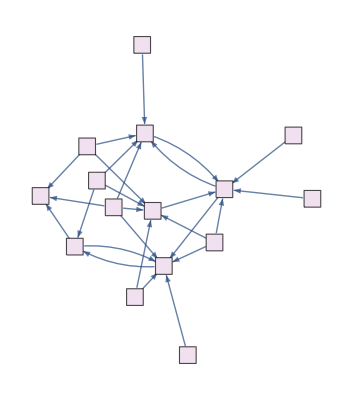

```mathematica
GraphPlot[Compativeis[Range[80,95],Range[81,95,2]],VertexStyle-> LightPurple,VertexShapeFunction->"Square",VertexSize->0.6, EdgeStyle->{Gray,Thick}, VertexLabels -> Placed[Automatic,Center], DirectedEdges->True]
```

### (b)

```mathematica
Manipulate[GraphPlot[Compativeis[Range[10j,10j+15],Range[10j+1,10j+15,2]], VertexStyle-> LightPurple,VertexShapeFunction->"Square",VertexSize->0.6, EdgeStyle->{Gray, Thick}, VertexLabels -> Placed[Automatic,Center], DirectedEdges->True],{j,1,10,1}]
```

GraphPlot::graph: A graph object is expected at position 1 in ….

## Problema 4

```mathematica
f[d_,n_]:=With[{x=Pick[d,Thread[Accumulate[d]-n<0]]},Scan[f[x,n-Total[#]]&,Subsets[Complement[d,x],{1,Infinity}]]]

f[_,0]:=Throw@True;

weird[n_]:=(DivisorSigma[1,n]>2 n)&&!TrueQ@Catch@f[Most@Divisors[n],n]
```

```mathematica
first4[]:=Module[{l,i},l={};i=1;While[Length[l]<4,If[OddQ[i]||Divisible[i,6],i++,If[weird[i],AppendTo[l,i]&&i++,i++]]];
Return[l]]
```

Determinação dos primeiros 4 números estranhos:

```mathematica
first4[]
```

{70,836,4030,5830}

O programa seguinte demora cerca de 23 minutos a correr. Confirma que não existem números estranhos da forma 70p, com 1299709 ≥ p ≥ 149 e primo.

```mathematica
a=70*Prime[Range[35,10^5]];
AbsoluteTiming[Select[Map[weird,a],False]]
```

{1378.79,{}}

## Problema 5

Dado um n, a função seguinte devolve, se existir, um par de naturais com metade dos dígitos de n, não ambos a terminar em 0, tais que os dígitos são precisamente os dígitos de n e cujo produto é n.

```mathematica
fatorizacoes[n_]:=Module[{potenciais=Select[Most@Divisors[n],IntegerLength[#]==IntegerLength[n]/2&],lista={}},If[Count[IntegerDigits[n],0]>(IntegerLength[n]/2),Return[{}],For[x=1,x<=Length[potenciais],x++,If[MemberQ[potenciais,n/potenciais[[x]]]&& MemberQ[Permutations[IntegerDigits[n]],Join[IntegerDigits[potenciais[[x]]],IntegerDigits[n/potenciais[[x]]]]]&&! MemberQ[lista,{(n/potenciais[[x]]),potenciais[[x]]}]&&!(Last[IntegerDigits[potenciais[[x]]]]==0&&Last[IntegerDigits[(n/potenciais[[x]])]]==0),AppendTo[lista,{potenciais[[x]],(n/potenciais[[x]])}]]];Return[lista]]]
AbsoluteTiming[fatorizacoes[1260]]
```

{0.0011504,{{21,60}}}

Lista de números que satisfazem as condições do enunciado com 2 dígitos:

```mathematica
l=Range[10,99];a={};
For[i=1,i≤Length[l],i++,If[Length[fatorizacoes[l[[i]]]]≠0,AppendTo[a,l[[i]]]]]
a
```

{}

Lista de números que satisfazem as condições do enunciado com 4 dígitos:

```mathematica
l=Range[1000,9999];a={};
For[i=1,i≤Length[l],i++,If[Length[fatorizacoes[l[[i]]]]≠0,AppendTo[a,l[[i]]]]];
a
```

{1260,1395,1435,1530,1827,2187,6880}

O programa seguinte demora cerca de 2 minutos a correr. Cálculo da quantidade de números com 6 dígitos que satisfazem as condições do enunciado:

```mathematica
l=Range[100000,999999];a={};
For[i=1,i≤Length[l],i++,If[Length[fatorizacoes[l[[i]]]]≠0,AppendTo[a,l[[i]]]]];
Length[a]
```

148

O programa seguinte não foi avaliado uma vez que demora horas a correr, tendo contado 701 números até ao momento em que se abortou a avaliação. Cálculo da quantidade de números com 8 dígitos que satisfazem as condições do enunciado:

```mathematica
l=Range[10000000,99999999];a={};
AbsoluteTiming[For[i=1,i≤Length[l],i++,If[Length[fatorizacoes[l[[i]]]]≠0,AppendTo[a,l[[i]]]]]]
Length[a]
```

$Aborted

701

## Problema 6

### (a)

```mathematica
Perrin[0]=3;
Perrin[1]=0;
Perrin[2]=2;
Perrin[n_Integer/;n>2]:=Perrin[n−2]+Perrin[n-3]
```

```mathematica
Solve[x^3-x-1==0]
```

{{x→Root1.32Root[-1-#1+#1^3&,1]1.324717957244746},{x→Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373},{x→Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373}}

```mathematica
r=Root"1.32"Root[-1-#1+#1^3&,1]1.324717957244746
q=Root"-0.662"-"0.562" ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373
s=Root"-0.662"+"0.562" ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373
```

Root1.32Root[-1-#1+#1^3&,1]1.324717957244746

Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373

Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373

```mathematica
Perrin1[n_Integer/;n>=0]:=Simplify[r^n+q^n+s^n]
```

```mathematica
Perrin[10]
```

17

```mathematica
Perrin1[10]
```

17

```mathematica
Perrin[30]
```

4610

```mathematica
Perrin1[30]
```

4610

```mathematica
Equivale[n_Integer/;n≥0]:=Equivalent[Perrin[n],Perrin1[n]]//TautologyQ
```

$Aborted

```mathematica
Equivale[5]
```

True

```mathematica
Lista=Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

O programa seguinte demora muito tempo a avaliar.

```mathematica
AllTrue[Range[1000],Equivale]
```

$Aborted

```mathematica
Perrin[0]
```

3

```mathematica
Perrin1[0]
```

3

```mathematica
FindInstance[Perrin[n]≠Perrin1[n] && n≥0,{n},Integers]
```

$Aborted

### (b)

```mathematica
A=({{0, 1, 0}, {0, 0, 1}, {1, 1, 0}});
```

```mathematica
Perrin2[n_Integer/;n>=0]:=(MatrixPower[A,n] .({{3}, {0}, {2}}))[[1,1]]
```

```mathematica
Perrin2[2]
```

2

```mathematica
Eigenvalues[A]
```

{Root1.32Root[-1-#1+#1^3&,1]1.324717957244746,Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373,Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373}

```mathematica
Equivalent[Perrin2[2],Perrin[2]]//TautologyQ
```

True

O programa seguinte demora muito tempo a avaliar.

```mathematica
Perrin2[10000000]
```

17156158769523967316026889319828669731223256412554304230969990804363134761635531503714726737472869694751366588544146610352055702484526570694823679886600429845122091977019881476975443469785717121350739607069322072183596093418016334355101736237036110676404557480330319420144283971005568251595218028567500130155791213526953125
 |  |  |  |

```mathematica
Equivale2[n_Integer/;n≥0]:=Equivalent[Perrin2[n],Perrin1[n]]//TautologyQ
```

O programa seguinte demora muito tempo a correr.

```mathematica
AllTrue[Range[1000],Equivale2]
```

$Aborted

```mathematica
FindInstance[Perrin[n]≠Perrin2[n] && n≥0,{n},Integers]
```

```mathematica
r
```

Root1.32Root[-1-#1+#1^3&,1]1.324717957244746

### (c)

```mathematica
r-FullSimplify[(1+r)^(1/3)]
```

0

```mathematica
Root"1.32"Root[-1-#1+#1^3&,1]1.324717957244746==(1+Root"1.32"Root[-1-#1+#1^3&,1]1.324717957244746)^(1/3)
```

Root1.32Root[-1-#1+#1^3&,1]1.324717957244746==(1+Root1.32Root[-1-#1+#1^3&,1]1.324717957244746)^(1/3)

### (d)

```mathematica
Limit[s^n,n->∞]
```

0

```mathematica
Limit[q^n,n->∞]
```

0

### (e)

```mathematica
DivisaoPerrin[n_Integer/;n≥0]:=Mod[Perrin2[n],n]==0
```

```mathematica
Lista2=Table[Prime[n],{n,10000}];
```

```mathematica
AllTrue[Lista2,DivisaoPerrin]
```

True

### (f)

```mathematica
PseudoPrimoP[n_Integer]:=And[CompositeQ[n],DivisaoPerrin[n]]
```

```mathematica
PseudoPrimoP[8]
```

False

```mathematica
PseudoPrimoP[13]
```

False

```mathematica
Module[{res={},x=1},
While[Length[res]<10,
If[ PseudoPrimoP[x] ,AppendTo[res,x],];
x++];
res]
```

$Aborted

```mathematica
PseudoPrimoP[271441]
```

True

```mathematica
PseudoPrimoP[904631]
```

True

```mathematica
PseudoPrimoP[16532714]
```

True

```mathematica
PseudoPrimoP[24658561]
```

True

```mathematica
PseudoPrimoP[27422714]
```

True

```mathematica
PseudoPrimoP[27664033]
```

True

```mathematica
PseudoPrimoP[46672291]
```

True

```mathematica
PseudoPrimoP[102690901]
```

True

```mathematica
PseudoPrimoP[130944133]
```

True

```mathematica
PseudoPrimoP[196075949]
```

True

## Problema 7

### (a)

```mathematica
Indices[n_Integer/;n>0]:=Reap[Module[{m=n,f=Fibonacci},
While[m>0,m-=f[Sow[NestWhile[#+1&,1,f[#]≤m&]-1]]]]][[2,-1]]
```

```mathematica
RepresentacaoZeckendorf[n_Integer/;n>0]:=Map[Fibonacci,Indices[n]]
```

```mathematica
RepresentacaoZeckendorfBinaria[n_Integer/;n>0]:=Module[{r=Indices[n],l=ConstantArray[0,Indices[n][[1]]]},For[i=1,i<Length[r]+1,i++,l=l=ReplacePart[l,r[[i]]->1]];l]
```

```mathematica
RepresentacaoZeckendorfBinaria[29]
```

{0,0,0,0,0,1,0,1}

```mathematica
Indices[29]
```

{8,6}

```mathematica
RepresentacaoZeckendorf[29]
```

{21,8}

```mathematica
RepresentacaoZeckendorf[8]
```

{8}

```mathematica
RepresentacaoZeckendorfBinaria[8]
```

{0,0,0,0,0,1}

```mathematica
Indices[8]
```

{6}

```mathematica
Zeckendorfinal[n_Integer/;n>0]:={Reverse[RepresentacaoZeckendorf[n]],Reverse[RepresentacaoZeckendorfBinaria[n]]}
```

```mathematica
Zeckendorfinal[19]
```

{{1,5,13},{1,0,1,0,0,1,0}}

```mathematica
Zeckendorfinal[8]
```

{{8},{1,0,0,0,0,0}}

{0,0,27,0,0,0,0,0,0,0}

O programa seguinte demora muito tempo a avaliar.

```mathematica
Lista1=Map[Zeckendorfinal,Range[1000000]]
```

{{{1},{1,0}},{{2},{1,0,0}},{{3},{1,0,0,0}},999995,{{2,5,13,34,144,46368,121393,832040},{1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,1,0,0}},{{55,144,46368,121393,832040},{1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0}}}
 |  |  |  |

```mathematica
Lista
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Comprimento2[w_]:=Length[w]==2
```

```mathematica
Comprimento2[{{3,4},{2}}]
```

True

O programa seguinte demora muito tempo a avaliar.

```mathematica
AllTrue[Lista1,Comprimento2]
```

True

### (b)

```mathematica
Soma[w_]:=Module[{res=0},For[i=1,i<Length[w]+1,i++,res=res+w[[i]]];res]
```

```mathematica
Soma[{2,4,7}]
```

13

```mathematica
Listanaoconsequtivos[w_]:=Not[MemberQ[Differences[w],1]]
```

```mathematica
Listanaoconsequtivos[{2,3,4}]
```

False

```mathematica
Listanaoconsequtivos[{1,3,5}]
```

True

```mathematica
EscolheListas[n_]:=Select[Subsets[Range[2,n]],Listanaoconsequtivos]
```

```mathematica
EscolheListas[5]
```

{{},{2},{3},{4},{5},{2,4},{2,5},{3,5}}

```mathematica
Fib[w_]:=Map[Fibonacci,w]
```

```mathematica
Fib[{2,3,6}]
```

{1,2,8}

```mathematica
SomaListasdeFib[n_]:=Map[Soma,Map[Fib,EscolheListas[n]]]
```

```mathematica
DuplicateFreeQ[SomaListasdeFib[8]]
```

True

## Problema 8

### (a)

```mathematica
intlist[n_,d_]:=Module[{r={},i=1,c=n}, While[i≤d,AppendTo[r,Mod[c,10]];i++;c=(c-Mod[c,10])/10];
Return[r]]
```

```mathematica
intlist[3,2]
```

{3,0}

Par é {n, d}, onde n  é um número natural e d  é o seu número de dígitos.

```mathematica
kaprekar[{n_,d_,b_}]:=If[DigitCount[n,b,Mod[n,b]]==d,Return[{}],Module[{maior=ReverseSort[intlist[n,d]],menor=Sort[intlist[n,d]]},a=FromDigits[maior]-FromDigits[menor];Return[{a,d,b}]]]
```

```mathematica
constantes[d_,b_]:=Module[{i,
lista={}},For[i=b^(d-1),i<(b^d)-1,i++,If[DigitCount[i,b,Mod[i,b]]==d,i++,If[kaprekar[{i,d,b}]=={i,d,b},AppendTo[lista,i]]]];
Return[lista]]
```

Qualquer que seja o número n escolhido, com 4 digítos, o algoritmo conduz sempre ao número 6174:

```mathematica
l={};
For[x=1000,x<9999,x++,If[DigitCount[x,10,Mod[x,10]]≠4&&FixedPoint[kaprekar,{x,4,10}]≠6174,AppendTo[l,x]]];
l
```

{}

### (b)

```mathematica
listatriplos[d_,b_]:=Module[{l={}}, For[x=b^(d-1),x<b^d-1,x++,If[DigitCount[x,b,Mod[x,b]]!=d,AppendTo[l,{x,d,b}]]];Return[l]]
```

```mathematica
Cicloslist[d_,b_]:=DeleteDuplicates[ciclos/@listatriplos[d,b]]
```

```mathematica
Cicloslist[2,10]
```

{{{9->81,81->63,63->27,27->45,45->9}},{{63->27,27->45,45->9,9->81,81->63}},{{27->45,45->9,9->81,81->63,63->27}},{{45->9,9->81,81->63,63->27,27->45}},{{81->63,63->27,27->45,45->9,9->81}}}

```mathematica
Cicloslist[3,10]
```

{{}}

```mathematica
Cicloslist[5,10]
```

{{{74943->62964,62964->71973,71973->83952,83952->74943}},{{63954->61974,61974->82962,82962->75933,75933->63954}},{{75933->63954,63954->61974,61974->82962,82962->75933}},{{83952->74943,74943->62964,62964->71973,71973->83952}},{{82962->75933,75933->63954,63954->61974,61974->82962}},{{61974->82962,82962->75933,75933->63954,63954->61974}},{{71973->83952,83952->74943,74943->62964,62964->71973}},{{62964->71973,71973->83952,83952->74943,74943->62964}},{{53955->59994,59994->53955}},{{59994->53955,53955->59994}}}

Os três programas seguintes não foram avaliados, demoram muito tempo a correr.

```mathematica
Cicloslist[6,10]
```

```mathematica
Cicloslist[7,10]
```

```mathematica
Cicloslist[8,10]
```